# SUGRA Base Classification

## LST Tensor Number / External / LST Gauge Algebra

## Setup

```mathematica
SetDirectory["~/Desktop/sugra_pipeline"];
Get["SUGRACatalog`"];
```

SUGRACatalog loaded.

entries = LoadCatalog["cat_1ext"]

CatalogSummary[entries]

ShowEntry[entries[[1]]]  (* copy-pasteable IF *)

FindEntries[entries, "e8"]

TMin[entry], TMax[entry]

## Define Classification Functions

```mathematica
(* NHC name -> gauge algebra name *)
nhcToGauge = <|
  "-3" -> "su3",
  "-4" -> "so8",
  "-5" -> "f4",
  "-6" -> "e6",
  "-7" -> "e7'",
  "-8" -> "e7",
  "-12" -> "e8",
  "-2-3" -> "su2+g2",
  "-2-4" -> "su2+so16",
  "-2-3-2" -> "su2+so7+su2",
  "-2-2-3" -> "sp1+g2",
  "pure-2" -> "",
  "???" -> "???"
|>;

nhcGaugeName[nhcName_String] := Lookup[nhcToGauge, nhcName, nhcName];

LSTGauge[entry_Association] := Module[
  {IF = entry["IF"], n, extIdxs, nonM1, visited, gauges = {}},
  n = Length[IF];
  extIdxs = ExtIndices[entry] + 1;
  nonM1 = Select[Range[n], IF[[#, #]] != -1 && !MemberQ[extIdxs, #] &];
  visited = Association[Thread[nonM1 -> False]];
  Do[
    If[!visited[s],
      Module[{comp = {}, queue = {s}},
        visited[s] = True;
        While[Length[queue] > 0,
          Module[{cur = First[queue]},
            queue = Rest[queue];
            AppendTo[comp, cur];
            Do[If[!visited[nb] && IF[[cur, nb]] != 0,
              visited[nb] = True; AppendTo[queue, nb]], {nb, nonM1}]]];
        comp = Sort[comp];
        Module[{subIF, nhcResult, gName},
          subIF = IF[[comp, comp]];
          nhcResult = NHCLookup[subIF];
          gName = nhcGaugeName[nhcResult["name"]];
          If[gName =!= "" && gName =!= Null,
            AppendTo[gauges, gName]]]]],
    {s, nonM1}];
  If[gauges === {}, "(none)",
    StringRiffle[Sort[gauges], " + "]]
];
```

```mathematica
ExtGauge[entry_Association] := Module[
  {exts = entry["externals"], gauges},
  gauges = Table[
    Switch[ext["extSI"],
      -2, "su2", -3, "su3", -4, "so8", -5, "f4",
      -6, "e6", -7, "e7'", -8, "e7", -12, "e8", -1, "hat1",
      _, ToString[ext["extSI"]]],
    {ext, exts}];
  StringRiffle[Sort[gauges], "+"]
];
```

## Load All Catalogs

### 1-ext

```mathematica
ext1 = Join @@ (LoadCatalog /@ Select[
  {"cat_1ext_t010","cat_1ext_t1120","cat_1ext_t2130","cat_1ext_t3140",
   "cat_1ext_t4150","cat_1ext_t5160","cat_1ext_t6170","cat_1ext_t7180",
   "cat_1ext_t8190","cat_1ext_t91100","cat_1ext_t101110",
   "cat_1ext_t111120","cat_1ext_t121130"}, DirectoryQ]);
```

Loaded 16247 entries from cat_1ext_t010

Loaded 29952 entries from cat_1ext_t1120

Loaded 17711 entries from cat_1ext_t2130

Loaded 8560 entries from cat_1ext_t3140

Loaded 4526 entries from cat_1ext_t4150

Loaded 2755 entries from cat_1ext_t5160

Loaded 947 entries from cat_1ext_t6170

Loaded 364 entries from cat_1ext_t7180

Loaded 152 entries from cat_1ext_t8190

Loaded 82 entries from cat_1ext_t91100

Loaded 31 entries from cat_1ext_t101110

Loaded 24 entries from cat_1ext_t111120

Loaded 17 entries from cat_1ext_t121130

### 2-ext ~ 6-ext

```mathematica
loadRange[prefix_, ranges_] := Join @@ (LoadCatalog /@ 
  Select[(prefix <> # &) /@ ranges, DirectoryQ]);
tranges = {"t010","t1120","t2130","t3140","t4150",
  "t5160","t6170","t7180","t8190","t91100"};
```

```mathematica
ext2 = loadRange["cat_2ext_", tranges];
```

Loaded 5934 entries from cat_2ext_t010

Loaded 7494 entries from cat_2ext_t1120

Loaded 3562 entries from cat_2ext_t2130

Loaded 1206 entries from cat_2ext_t3140

Loaded 744 entries from cat_2ext_t4150

Loaded 116 entries from cat_2ext_t5160

Loaded 25 entries from cat_2ext_t6170

Loaded 3 entries from cat_2ext_t7180

Loaded 1 entries from cat_2ext_t8190

Loaded 0 entries from cat_2ext_t91100

```mathematica
ext3 = loadRange["cat_3ext_", tranges];
```

Loaded 2636 entries from cat_3ext_t010

Loaded 1104 entries from cat_3ext_t1120

Loaded 149 entries from cat_3ext_t2130

Loaded 43 entries from cat_3ext_t3140

Loaded 17 entries from cat_3ext_t4150

Loaded 0 entries from cat_3ext_t5160

Loaded 0 entries from cat_3ext_t6170

Loaded 0 entries from cat_3ext_t7180

Loaded 0 entries from cat_3ext_t8190

Loaded 0 entries from cat_3ext_t91100

```mathematica
ext4 = loadRange["cat_4ext_", tranges];
```

Loaded 578 entries from cat_4ext_t010

Loaded 90 entries from cat_4ext_t1120

Loaded 3 entries from cat_4ext_t2130

Loaded 19 entries from cat_4ext_t3140

Loaded 3 entries from cat_4ext_t4150

```mathematica
ext5 = loadRange["cat_5ext_", tranges];
```

Loaded 71 entries from cat_5ext_t010

Loaded 3 entries from cat_5ext_t1120

Loaded 0 entries from cat_5ext_t2130

```mathematica
ext6 = loadRange["cat_6ext_", tranges];
```

Loaded 17 entries from cat_6ext_t010

Loaded 0 entries from cat_6ext_t1120

### NHC ext

```mathematica
nhcExt = Join @@ (LoadCatalog /@ Select[
  {"cat_nhc_ext","cat_nhc_ext_2ext","cat_nhc_ext_3ext",
   "cat_nhc_ext_4ext","cat_nhc_ext_5ext","cat_nhc_ext_6ext",
   "cat_nhc_ext_7ext"}, DirectoryQ]);
```

Loaded 2131 entries from cat_nhc_ext

Loaded 358 entries from cat_nhc_ext_2ext

Loaded 97 entries from cat_nhc_ext_3ext

Loaded 17 entries from cat_nhc_ext_4ext

Loaded 1 entries from cat_nhc_ext_5ext

Loaded 25 entries from cat_nhc_ext_6ext

Loaded 1 entries from cat_nhc_ext_7ext

### Merge all

```mathematica
allExt = Join[ext1, ext2, ext3, ext4, ext5, ext6, nhcExt];
Print["Total entries: ", Length[allExt]];
```

Total entries: 107816

## Entry Count Summary

```mathematica
Grid[{
  {Style["Category", Bold], Style["Count", Bold]},
  {"1-ext", Length[ext1]},
  {"2-ext", Length[ext2]},
  {"3-ext", Length[ext3]},
  {"4-ext", Length[ext4]},
  {"5-ext", Length[ext5]},
  {"6-ext", Length[ext6]},
  {"NHC ext", Length[nhcExt]},
  {Style["Total", Bold], Style[Length[allExt], Bold]}
}, Frame -> All]
```

Category | Count
1-ext | 81368
2-ext | 19085
3-ext | 3949
4-ext | 693
5-ext | 74
6-ext | 17
NHC ext | 2630
Total | 107816

## Compute Classification (T_LST, External, LST Gauge)

This may take a few minutes for large catalogs.

```mathematica
classData = Monitor[
  Table[With[{e = allExt[[i]]},
    <|"T" -> e["baseT"],
      "extGauge" -> ExtGauge[e],
      "lstGauge" -> LSTGauge[e],
      "Tsugra" -> e["T"],
      "det" -> e["det"],
      "uni" -> (Abs[e["det"]] == 1)|>],
    {i, Length[allExt]}],
  ProgressIndicator[i, {1, Length[allExt]}]
];
```

### Classification Table

```mathematica
groups = GroupBy[classData, {#["T"], #["extGauge"], #["lstGauge"]} &];
classTable = SortBy[
  KeyValueMap[
    <|"T_LST" -> #1[[1]], "External" -> #1[[2]],
      "LST_Gauge" -> #1[[3]], "Count" -> Length[#2],
      "T_range" -> MinMax[#2[[All, "Tsugra"]]]|> &,
    groups],
  {#["T_LST"], -#["Count"]} &
];
```

```mathematica
Dataset[classTable[[;; Min[50, Length[classTable]]]]]
```

### Summary by T_LST

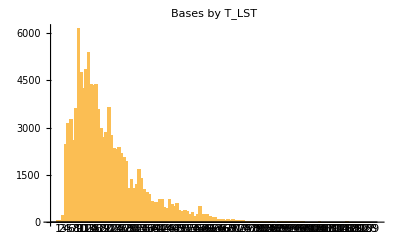

```mathematica
tSummary = SortBy[
  KeyValueMap[{#1, Length[#2]} &, GroupBy[classData, #["T"] &]],
  First];
BarChart[tSummary[[All, 2]], ChartLabels -> tSummary[[All, 1]],
  PlotLabel -> "Bases by T_LST"]
```

### Summary by External Gauge

```mathematica
extSummary = ReverseSortBy[
  KeyValueMap[{#1, Length[#2]} &, GroupBy[classData, #["extGauge"] &]],
  Last];
Grid[Prepend[extSummary,
  {Style["External", Bold], Style["Count", Bold]}],
  Frame -> All]
```

External | Count
su2 | 54361
su3 | 11173
su2+su2 | 9561
su2+su3 | 4418
so8 | 4182
f4 | 3839
e6 | 2865
su2+su2+su2 | 2697
e7 | 2132
e7' | 1873
su2+su2+su3 | 1240
su3+su3 | 1108
e8 | 919
so8+su2 | 719
f4+su3 | 660
f4+su2 | 611
so8+su3 | 609
su2+su2+su2+su2 | 461
e6+su2 | 441
f4+so8 | 339
e6+su3 | 320
su2+su2+su2+su3 | 246
so8+so8 | 202
e7+su3 | 201
e7+su2 | 192
f4+f4 | 186
e7'+su3 | 170
e7'+su2 | 144
su2+su3+su3 | 143
so8+su2+su2 | 127
e6+f4 | 124
e6+so8 | 121
e7+so8 | 106
e7'+so8 | 92
e7+f4 | 90
e7'+f4 | 87
e6+e7 | 71
e6+e7' | 68
e6+e6 | 62
su3+su3+su3 | 54
so8+su2+su2+su2 | 53
e7+e7' | 51
e7+e7 | 44
su2+su2+su2+su2+su2 | 43
so8+su2+su3 | 42
e8+su3 | 31
e7'+e7' | 30
su2+su2+su2+su2+su3 | 29
e8+f4 | 28
su2+su2+su3+su3 | 27
su2+su2+su2+su2+su2+su3+su3 | 24
so8+su2+su2+su3 | 24
hat1 | 24
hat1+su2 | 23
e8+so8 | 22
e6+e8 | 22
e6+su2+su2 | 21
e7'+su2+su3 | 18
f4+su2+su2 | 17
e7'+su2+su2 | 17
e7'+e8 | 16
e7+e8 | 15
so8+so8+su2 | 14
e6+su2+su3 | 13
su2+su2+su2+su2+su2+su2 | 12
e8+su2 | 12
so8+su3+su3 | 11
su2+su2+su2+su3+su3 | 10
e7'+so8+su2 | 10
so8+su2+su2+su2+su2 | 8
e8+e8 | 8
e6+so8+su2 | 7
e7+su2+su2 | 6
e6+f4+su2 | 6
su2+su2+su2+su2+su3+su3 | 5
f4+su2+su3 | 5
hat1+su3 | 4
e7+su2+su3 | 4
e6+su2+su2+su2 | 4
hat1+su2+su2 | 3
f4+su2+su2+su2 | 3
e6+hat1 | 3
su2+su2+su2+su2+su2+su3 | 2
so8+su2+su2+su2+su2+su2 | 2
f4+su3+su3 | 2
f4+hat1 | 2
f4+f4+su2 | 2
e7+su2+su2+su2 | 2
e7'+hat1+su3 | 2
e6+hat1+su3 | 2
su2+su3+su3+su3 | 1
su2+su2+su2+su2+su2+su2+su3 | 1
su2+su2+su2+su2+su2+su2+su2+su3 | 1
so8+su2+su3+su3 | 1
so8+su2+su2+su2+su3 | 1
so8+so8+su3 | 1
so8+so8+su2+su2 | 1
so8+so8+so8+su2 | 1
hat1+so8+so8+su2 | 1
hat1+so8 | 1
hat1+hat1+su2 | 1
f4+f4+su2+su2 | 1
e7'+su2+su2+su2 | 1
e7+hat1+su3 | 1
e7+hat1+so8 | 1
e6+su2+su2+su2+su2 | 1
e6+e6+su2 | 1

### Summary by LST Gauge (top 30)

```mathematica
lstSummary = ReverseSortBy[
  KeyValueMap[{#1, Length[#2]} &, GroupBy[classData, #["lstGauge"] &]],
  Last];
Grid[Prepend[lstSummary[[;; Min[30, Length[lstSummary]]]],
  {Style["LST Gauge", Bold], Style["Count", Bold]}],
  Frame -> All]
```

LST Gauge | Count
e6 + e6 + e6 + su3 + su3 | 1849
e6 + f4 + su3 | 1634
e6 + e6 + f4 + su3 + su3 | 1293
f4 | 1274
e6 | 1227
su2+g2 + su3 | 895
e6 + e6 + e6 + f4 + su3 + su3 + su3 | 860
e6 + f4 + su2+g2 | 847
su3 + su3 | 836
e6 + e6 + su2+so7+su2 | 778
so8 | 742
so8 + so8 | 675
e6 + e6 + e7 + su2+so7+su2 + su2+so7+su2 | 633
e6 + e6 + su3 | 568
so8 + su2+g2 + su3 | 558
e6 + e7 + f4 + su2+g2 + su2+so7+su2 | 556
e6 + e6 + e6 + e6 + f4 + su3 + su3 + su3 + su3 | 519
e6 + e6 + e7 + e7 + su2+so7+su2 + su2+so7+su2 + su2+so7+su2 | 517
e7 + f4 + sp1+g2 | 513
e6 + e7 + e7 + f4 + su2+g2 + su2+so7+su2 + su2+so7+su2 | 473
e6 + e6 + e7 + e7 + e7 + su2+so7+su2 + su2+so7+su2 + su2+so7+su2 + su2+so7+su2 | 428
(none) | 426
e6 + f4 + sp1+g2 | 424
e6 + e7 + e7 + e7 + f4 + su2+g2 + su2+so7+su2 + su2+so7+su2 + su2+so7+su2 | 422
e6 + e6 + e6 + e6 + e6 + f4 + su3 + su3 + su3 + su3 + su3 | 411
e6 + e6 + e6 + su2+so7+su2 + su3 | 395
e6 + e6 + e7 + e7 + e7 + e7 + su2+so7+su2 + su2+so7+su2 + su2+so7+su2 + su2+so7+su2 + su2+so7+su2 | 380
e7 + f4 + su2+g2 | 372
e6 + e6 + e6 + su3 + su3 + su3 | 371
so8 + so8 + so8 | 366

## Unimodular vs Non-unimodular

```mathematica
uniCount = Count[classData, _?(#["uni"] &)];
nonuniCount = Length[classData] - uniCount;
PieChart[{uniCount, nonuniCount},
  ChartLabels -> {"Uni (" <> ToString[uniCount] <> ")",
    "Non-uni (" <> ToString[nonuniCount] <> ")"},
  PlotLabel -> "Determinant Distribution"]
```

-Graphics-

## Search Examples

```mathematica
(* Find all bases with e8 in LST gauge *)
e8Bases = Select[allExt, StringContainsQ[LSTGauge[#], "e8"] &];
Print["e8 bases: ", Length[e8Bases]]
```

```mathematica
(* Find bases with hat1 external *)
hat1Bases = Select[allExt, StringContainsQ[ExtGauge[#], "hat1"] &];
Print["hat1 bases: ", Length[hat1Bases]]
```

hat1 bases: 68

```mathematica
(* Show first result *)
If[Length[e8Bases] > 0, ShowEntry[e8Bases[[1]]]]
```

## Export to CSV

```mathematica
Export["classification.csv",
  Prepend[
    Table[{c["T_LST"], c["External"], c["LST_Gauge"], c["Count"]},
      {c, classTable}],
    {"T_LST", "External", "LST_Gauge", "Count"}]];
Print["Exported to classification.csv"]
```

Exported to classification.csv